```mathematica
ClearAll["Global`*"]
```

### Pion

```mathematica
idealπ=
{{7.17752430*10^-03,2.18980123*10^+02},{3.78993630*10^-02,2.18639053*10^+02},{9.35073360*10^-02,2.13122813*10^+02},{1.74611500*10^-01,1.87502522*10^+02},{2.82124830*10^-01,1.40816711*10^+02},{4.17333600*10^-01,9.17229312*10^+01},{5.81993540*10^-01,5.33718276*10^+01},{7.78479140*10^-01,2.81854113*10^+01},{1.01002170*10^+00,1.35314490*10^+01},{1.28110830*10^+00,5.85498876*10^+00},{1.59819070*10^+00,2.24466924*10^+00},{1.97106870*10^+00,7.41926889*10^-01},{2.41596300*10^+00,2.02085807*10^-01},{2.96389860*10^+00,4.16237710*10^-02}(*,{3.69431420*10^+00,5.20294673*10^-03}*)};


shear14π={{7.17752430*10^-03,2.18941609*10^+02},{3.78993630*10^-02,2.18475028*10^+02},{9.35073360*10^-02,2.12482537*10^+02},{1.74611500*10^-01,1.86294262*10^+02},{2.82124830*10^-01,1.39469211*10^+02},{4.17333600*10^-01,9.06810759*10^+01},{5.81993540*10^-01,5.27974970*10^+01},{7.78479140*10^-01,2.80047913*10^+01},{1.01002170*10^+00,1.35767643*10^+01},{1.28110830*10^+00,5.97430037*10^+00},{1.59819070*10^+00,2.34985823*10^+00},{1.97106870*10^+00,8.05424170*10^-01},{2.41596300*10^+00,2.30489415*10^-01},{2.96389860*10^+00,5.07293523*10^-02}(*,{3.69431420*10^+00,6.95914088*10^-03}*)};

shearCEπ=
{{7.17752430*10^-03,2.19809107*10^+02},{3.78993630*10^-02,2.18628923*10^+02},{9.35073360*10^-02,2.10295605*10^+02},{1.74611500*10^-01,1.82504816*10^+02},{2.82124830*10^-01,1.36547711*10^+02},{4.17333600*10^-01,8.93767572*10^+01},{5.81993540*10^-01,5.26018957*10^+01},{7.78479140*10^-01,2.82617661*10^+01},{1.01002170*10^+00,1.38791827*10^+01},{1.28110830*10^+00,6.17246886*10^+00},{1.59819070*10^+00,2.44181264*10^+00},{1.97106870*10^+00,8.35470607*10^-01},{2.41596300*10^+00,2.36207536*10^-01},{2.96389860*10^+00,5.06498596*10^-02}(*,{3.69431420*10^+00,6.62814423*10^-03}*)};

shearmodπ ={{7.17752430*10^-03,2.19468203*10^+02},{3.78993630*10^-02,2.18479602*10^+02},{9.35073360*10^-02,2.10708864*10^+02},{1.74611500*10^-01,1.83101281*10^+02},{2.82124830*10^-01,1.36729494*10^+02},{4.17333600*10^-01,8.91567036*10^+01},{5.81993540*10^-01,5.22365786*10^+01},{7.78479140*10^-01,2.79425458*10^+01},{1.01002170*10^+00,1.36736840*10^+01},{1.28110830*10^+00,6.06813954*10^+00},{1.59819070*10^+00,2.40014995*10^+00},{1.97106870*10^+00,8.23227763*10^-01},{2.41596300*10^+00,2.34151348*10^-01},{2.96389860*10^+00,5.07809141*10^-02}(*,{3.69431420*10^+00,6.78443278*10^-03}*)};

bulk14π = {{7.17752430*10^-03,2.16497031*10^+02},{3.78993630*10^-02,2.16180214*10^+02},{9.35073360*10^-02,2.10656696*10^+02},{1.74611500*10^-01,1.84637411*10^+02},{2.82124830*10^-01,1.37246064*10^+02},{4.17333600*10^-01,8.78131115*10^+01},{5.81993540*10^-01,4.97764052*10^+01},{7.78479140*10^-01,2.53384548*10^+01},{1.01002170*10^+00,1.15443413*10^+01},{1.28110830*10^+00,4.62497266*10^+00},{1.59819070*10^+00,1.57543207*10^+00},{1.97106870*10^+00,4.28814659*10^-01},{2.41596300*10^+00,8.09880198*10^-02},{2.96389860*10^+00,5.74322286*10^-03}};

bulkCEπ=
{{7.17752430*10^-03,2.13953927*10^+02},{3.78993630*10^-02,2.13723431*10^+02},{9.35073360*10^-02,2.08025718*10^+02},{1.74611500*10^-01,1.80207263*10^+02},{2.82124830*10^-01,1.30917869*10^+02},{4.17333600*10^-01,8.17095584*10^+01},{5.81993540*10^-01,4.53202768*10^+01},{7.78479140*10^-01,2.26681298*10^+01},{1.01002170*10^+00,1.02029799*10^+01},{1.28110830*10^+00,4.07541290*10^+00},{1.59819070*10^+00,1.40948228*10^+00},{1.97106870*10^+00,4.05677550*10^-01},{2.41596300*10^+00,9.06590825*10^-02},{2.96389860*10^+00,1.35734791*10^-02}};

bulkmodπ=
{{7.17752430*10^-03,2.13914409*10^+02},{3.78993630*10^-02,2.13667120*10^+02},{9.35073360*10^-02,2.07860499*10^+02},{1.74611500*10^-01,1.79686608*10^+02},{2.82124830*10^-01,1.30152040*10^+02},{4.17333600*10^-01,8.11139644*10^+01},{5.81993540*10^-01,4.50193301*10^+01},{7.78479140*10^-01,2.25850738*10^+01},{1.01002170*10^+00,1.02315918*10^+01},{1.28110830*10^+00,4.13825694*10^+00},{1.59819070*10^+00,1.46499214*10^+00},{1.97106870*10^+00,4.40302022*10^-01},{2.41596300*10^+00,1.06888281*10^-01},{2.96389860*10^+00,1.90689743*10^-02}};


shearbulk14π={{7.17752430*10^-03,2.16458516*10^+02},{3.78993630*10^-02,2.16016189*10^+02},{9.35073360*10^-02,2.10016420*10^+02},{1.74611500*10^-01,1.83429152*10^+02},{2.82124830*10^-01,1.35898565*10^+02},{4.17333600*10^-01,8.67712561*10^+01},{5.81993540*10^-01,4.92020746*10^+01},{7.78479140*10^-01,2.51578348*10^+01},{1.01002170*10^+00,1.15896566*10^+01},{1.28110830*10^+00,4.74428427*10^+00},{1.59819070*10^+00,1.68062105*10^+00},{1.97106870*10^+00,4.92311940*10^-01},{2.41596300*10^+00,1.09391628*10^-01},{2.96389860*10^+00,1.48488042*10^-02}};

(*shearbulk14test = Table[{idealπ[[i,1]], shear14π[[i,2]]+bulk14π[[i,2]]-idealπ[[i,2]]},{i,1,Length[idealπ]}]*)

shearbulkCEπ={{7.17752430*10^-03,2.14782910*10^+02},{3.78993630*10^-02,2.13713300*10^+02},{9.35073360*10^-02,2.05198510*10^+02},{1.74611500*10^-01,1.75209558*10^+02},{2.82124830*10^-01,1.26648869*10^+02},{4.17333600*10^-01,7.93633844*10^+01},{5.81993540*10^-01,4.45503449*10^+01},{7.78479140*10^-01,2.27444846*10^+01},{1.01002170*10^+00,1.05507135*10^+01},{1.28110830*10^+00,4.39289300*10^+00},{1.59819070*10^+00,1.60662568*10^+00},{1.97106870*10^+00,4.99221267*10^-01},{2.41596300*10^+00,1.24780811*10^-01},{2.96389860*10^+00,2.25995677*10^-02}};

shearbulkmodπ={{7.17752430*10^-03,2.14778952*10^+02},{3.78993630*10^-02,2.13825242*10^+02},{9.35073360*10^-02,2.05566730*10^+02},{1.74611500*10^-01,1.75659235*10^+02},{2.82124830*10^-01,1.26986075*10^+02},{4.17333600*10^-01,7.96395107*10^+01},{5.81993540*10^-01,4.47674828*10^+01},{7.78479140*10^-01,2.28872393*10^+01},{1.01002170*10^+00,1.06315501*10^+01},{1.28110830*10^+00,4.43649966*10^+00},{1.59819070*10^+00,1.63082326*10^+00},{1.97106870*10^+00,5.12487100*10^-01},{2.41596300*10^+00,1.31177917*10^-01},{2.96389860*10^+00,2.49738431*10^-02}};

(*shearbulkmodπregdetA {{7.17752430e-03,2.67804109e+02},{3.78993630e-02,2.64649412e+02},{9.35073360e-02,2.55080929e+02},{1.74611500e-01,2.23498262e+02},{2.82124830e-01,1.69008216e+02},{4.17333600e-01,1.12183366e+02},{5.81993540e-01,6.67095239e+01},{7.78479140e-01,3.55348951e+01},{1.01002170e+00,1.67495157e+01},{1.28110830e+00,6.87702899e+00},{1.59819070e+00,2.41752721e+00},{1.97106870e+00,7.11204709e-01},{2.41596300e+00,1.68406910e-01},{2.96389860e+00,2.95959721e-02}}*)

(*shearbulkmodπNoRegulation={7.17752430e-03,2.13420307e+02},{3.78993630e-02,2.12458591e+02},{9.35073360e-02,2.04074232e+02},{1.74611500e-01,1.74041151e+02},{2.82124830e-01,1.25477438e+02},{4.17333600e-01,7.84376533e+01},{5.81993540e-01,4.39522658e+01},{7.78479140e-01,2.24206265e+01},{1.01002170e+00,1.04083907e+01},{1.28110830e+00,4.34804535e+00},{1.59819070e+00,1.60209146e+00},{1.97106870e+00,5.05040498e-01},{2.41596300e+00,1.29718117e-01},{2.96389860e+00,2.47802770e-02}*)
```

### Kaon

```mathematica
idealK={{7.17752430*10^-03,2.01394732*10^+01},{3.78993630*10^-02,2.01350865*10^+01},{9.35073360*10^-02,2.01000980*10^+01},{1.74611500*10^-01,1.98985679*10^+01},{2.82124830*10^-01,1.90960770*10^+01},{4.17333600*10^-01,1.70334534*10^+01},{5.81993540*10^-01,1.35283657*10^+01},{7.78479140*10^-01,9.33466609*10^+00},{1.01002170*10^+00,5.55351147*10^+00},{1.28110830*10^+00,2.84190147*10^+00},{1.59819070*10^+00,1.24239066*10^+00},{1.97106870*10^+00,4.55767592*10^-01},{2.41596300*10^+00,1.35109755*10^-01},{2.96389860*10^+00,2.98755010*10^-02}};

shear14K = {{7.17752430*10^-03,2.03297632*10^+01},{3.78993630*10^-02,2.03167915*10^+01},{9.35073360*10^-02,2.02383084*10^+01},{1.74611500*10^-01,1.99278926*10^+01},{2.82124830*10^-01,1.89640382*10^+01},{4.17333600*10^-01,1.67729989*10^+01},{5.81993540*10^-01,1.32567043*10^+01},{7.78479140*10^-01,9.15706085*10^+00},{1.01002170*10^+00,5.49331048*10^+00},{1.28110830*10^+00,2.85812960*10^+00},{1.59819070*10^+00,1.28257238*10^+00},{1.97106870*10^+00,4.88390735*10^-01},{2.41596300*10^+00,1.52308575*10^-01},{2.96389860*10^+00,3.60427179*10^-02}};

shearCEK={{7.17752430*10^-03,2.05732878*10^+01},{3.78993630*10^-02,2.05500390*10^+01},{9.35073360*10^-02,2.04198812*10^+01},{1.74611500*10^-01,1.99826800*10^+01},{2.82124830*10^-01,1.88420771*10^+01},{4.17333600*10^-01,1.65379513*10^+01},{5.81993540*10^-01,1.30566894*10^+01},{7.78479140*10^-01,9.07924594*10^+00},{1.01002170*10^+00,5.51043527*10^+00},{1.28110830*10^+00,2.90247966*10^+00},{1.59819070*10^+00,1.31387053*10^+00},{1.97106870*10^+00,5.01041848*10^-01},{2.41596300*10^+00,1.54831950*10^-01},{2.96389860*10^+00,3.57872385*10^-02}};

shearmodK={{7.17752430*10^-03,2.05498289*10^+01},{3.78993630*10^-02,2.05303700*10^+01},{9.35073360*10^-02,2.04193769*10^+01},{1.74611500*10^-01,2.00260073*10^+01},{2.82124830*10^-01,1.89336369*10^+01},{4.17333600*10^-01,1.66327078*10^+01},{5.81993540*10^-01,1.30971690*10^+01},{7.78479140*10^-01,9.05796886*10^+00},{1.01002170*10^+00,5.46332071*10^+00},{1.28110830*10^+00,2.86279902*10^+00},{1.59819070*10^+00,1.29218687*10^+00},{1.97106870*10^+00,4.92934214*10^-01},{2.41596300*10^+00,1.53017021*10^-01},{2.96389860*10^+00,3.57371964*10^-02}};

bulk14K = {{7.17752430*10^-03,2.01576687*10^+01},{3.78993630*10^-02,2.01543246*10^+01},{9.35073360*10^-02,2.01237524*10^+01},{1.74611500*10^-01,1.99267592*10^+01},{2.82124830*10^-01,1.91040709*10^+01},{4.17333600*10^-01,1.69564647*10^+01},{5.81993540*10^-01,1.33023187*10^+01},{7.78479140*10^-01,8.96609962*10^+00},{1.01002170*10^+00,5.12854576*10^+00},{1.28110830*10^+00,2.46506397*10^+00},{1.59819070*10^+00,9.75731143*10^-01},{1.97106870*10^+00,3.03903445*10^-01},{2.41596300*10^+00,6.68006021*10^-02},{2.96389860*10^+00,7.05603977*10^-03}};

bulkCEK={{7.17752430*10^-03,2.06309555*10^+01},{3.78993630*10^-02,2.06289065*10^+01},{9.35073360*10^-02,2.06047002*10^+01},{1.74611500*10^-01,2.04216548*10^+01},{2.82124830*10^-01,1.96041565*10^+01},{4.17333600*10^-01,1.73981458*10^+01},{5.81993540*10^-01,1.35841330*10^+01},{7.78479140*10^-01,9.05801280*10^+00},{1.01002170*10^+00,5.10818263*10^+00},{1.28110830*10^+00,2.42736127*10^+00},{1.59819070*10^+00,9.62148357*10^-01},{1.97106870*10^+00,3.09969587*10^-01},{2.41596300*10^+00,7.67735054*10^-02},{2.96389860*10^+00,1.29025486*10^-02}};

bulkmodK={{7.17752430*10^-03,2.07263218*10^+01},{3.78993630*10^-02,2.07236235*10^+01},{9.35073360*10^-02,2.06965249*10^+01},{1.74611500*10^-01,2.05091372*10^+01},{2.82124830*10^-01,1.96910940*10^+01},{4.17333600*10^-01,1.74765841*10^+01},{5.81993540*10^-01,1.36174918*10^+01},{7.78479140*10^-01,9.03375155*10^+00},{1.01002170*10^+00,5.06408426*10^+00},{1.28110830*10^+00,2.39966238*10^+00},{1.59819070*10^+00,9.56229492*10^-01},{1.97106870*10^+00,3.14523328*10^-01},{2.41596300*10^+00,8.19428698*10^-02},{2.96389860*10^+00,1.54806657*10^-02}};

shearbulk14K = {{7.17752430*10^-03,2.03479587*10^+01},{3.78993630*10^-02,2.03360296*10^+01},{9.35073360*10^-02,2.02619629*10^+01},{1.74611500*10^-01,1.99560839*10^+01},{2.82124830*10^-01,1.89720320*10^+01},{4.17333600*10^-01,1.66960103*10^+01},{5.81993540*10^-01,1.30306572*10^+01},{7.78479140*10^-01,8.78849438*10^+00},{1.01002170*10^+00,5.06834476*10^+00},{1.28110830*10^+00,2.48129210*10^+00},{1.59819070*10^+00,1.01591287*10^+00},{1.97106870*10^+00,3.36526589*10^-01},{2.41596300*10^+00,8.39994218*10^-02},{2.96389860*10^+00,1.32232567*10^-02}};

shearbulkCEK={{7.17752430*10^-03,2.10647700*10^+01},{3.78993630*10^-02,2.10438590*10^+01},{9.35073360*10^-02,2.09244834*10^+01},{1.74611500*10^-01,2.05057668*10^+01},{2.82124830*10^-01,1.93501567*10^+01},{4.17333600*10^-01,1.69026438*10^+01},{5.81993540*10^-01,1.31124567*10^+01},{7.78479140*10^-01,8.80259266*10^+00},{1.01002170*10^+00,5.06510642*10^+00},{1.28110830*10^+00,2.48793946*10^+00},{1.59819070*10^+00,1.03362823*10^+00},{1.97106870*10^+00,3.55243843*10^-01},{2.41596300*10^+00,9.64957001*10^-02},{2.96389860*10^+00,1.88142861*10^-02}};

shearbulkmodK = {{7.17752430*10^-03,2.12054743*10^+01},{3.78993630*10^-02,2.11928366*10^+01},{9.35073360*10^-02,2.10980393*10^+01},{1.74611500*10^-01,2.07290106*10^+01},{2.82124830*10^-01,1.96358792*10^+01},{4.17333600*10^-01,1.72141151*10^+01},{5.81993540*10^-01,1.33687409*10^+01},{7.78479140*10^-01,8.95258761*10^+00},{1.01002170*10^+00,5.12634513*10^+00},{1.28110830*10^+00,2.50540041*10^+00},{1.59819070*10^+00,1.03809498*10^+00},{1.97106870*10^+00,3.57771320*10^-01},{2.41596300*10^+00,9.85095345*10^-02},{2.96389860*10^+00,1.99067341*10^-02}};
```

### Proton

```mathematica
idealp={{7.17752430*10^-03,2.19371761*10^+00},{3.78993630*10^-02,2.19356603*10^+00},{9.35073360*10^-02,2.19265342*10^+00},{1.74611500*10^-01,2.18884569*10^+00},{2.82124830*10^-01,2.17465771*10^+00},{4.17333600*10^-01,2.12895353*10^+00},{5.81993540*10^-01,2.00962905*10^+00},{7.78479140*10^-01,1.76707139*10^+00},{1.01002170*10^+00,1.39041395*10^+00},{1.28110830*10^+00,9.44417508*10^-01},{1.59819070*10^+00,5.38093902*10^-01},{1.97106870*10^+00,2.50303241*10^-01},{2.41596300*10^+00,9.14990735*10^-02},{2.96389860*10^+00,2.43807560*10^-02}(*,{3.69431420*10^+00,3.86378588*10^-03}*)};

shear14p ={{7.17752430*10^-03,2.23656213*10^+00},{3.78993630*10^-02,2.23574387*10^+00},{9.35073360*10^-02,2.23138010*10^+00},{1.74611500*10^-01,2.21793867*10^+00},{2.82124830*10^-01,2.18516179*10^+00},{4.17333600*10^-01,2.11364885*10^+00},{5.81993540*10^-01,1.97065175*10^+00},{7.78479140*10^-01,1.71944816*10^+00},{1.01002170*10^+00,1.35391784*10^+00},{1.28110830*10^+00,9.29407638*10^-01},{1.59819070*10^+00,5.40404452*10^-01},{1.97106870*10^+00,2.58926839*10^-01},{2.41596300*10^+00,9.83951658*10^-02},{2.96389860*10^+00,2.75324980*10^-02}(*,{3.69431420*10^+00,4.64887197*10^-03}*)};

shearCEp={{7.17752430*10^-03,2.24621773*10^+00},{3.78993630*10^-02,2.24526959*10^+00},{9.35073360*10^-02,2.24023166*10^+00},{1.74611500*10^-01,2.22489309*10^+00},{2.82124830*10^-01,2.18840589*10^+00},{4.17333600*10^-01,2.11172599*10^+00},{5.81993540*10^-01,1.96436510*10^+00},{7.78479140*10^-01,1.71284422*10^+00},{1.01002170*10^+00,1.35146961*10^+00},{1.28110830*10^+00,9.31532844*10^-01},{1.59819070*10^+00,5.43684886*10^-01},{1.97106870*10^+00,2.60562713*10^-01},{2.41596300*10^+00,9.83834769*10^-02},{2.96389860*10^+00,2.70902735*10^-02}(*,{3.69431420*10^+00,4.43783380*10^-03}*)};

shearmodp={{7.17752430*10^-03,2.25053468*10^+00},{3.78993630*10^-02,2.24975306*10^+00},{9.35073360*10^-02,2.24555456*10^+00},{1.74611500*10^-01,2.23246613*10^+00},{2.82124830*10^-01,2.19991824*10^+00},{4.17333600*10^-01,2.12751313*10^+00},{5.81993540*10^-01,1.98155045*10^+00},{7.78479140*10^-01,1.72615605*10^+00},{1.01002170*10^+00,1.35754775*10^+00},{1.28110830*10^+00,9.31877834*10^-01},{1.59819070*10^+00,5.42308296*10^-01},{1.97106870*10^+00,2.59955796*10^-01},{2.41596300*10^+00,9.86292645*10^-02},{2.96389860*10^+00,2.74599376*10^-02}(*,{3.69431420*10^+00,4.59195262*10^-03}*)};

bulk14p = {{7.17752430*10^-03,2.35387876*10^+00},{3.78993630*10^-02,2.35378686*10^+00},{9.35073360*10^-02,2.35319659*10^+00},{1.74611500*10^-01,2.35039865*10^+00},{2.82124830*10^-01,2.33850975*10^+00},{4.17333600*10^-01,2.29595587*10^+00},{5.81993540*10^-01,2.17530920*10^+00},{7.78479140*10^-01,1.91467258*10^+00},{1.01002170*10^+00,1.49425336*10^+00},{1.28110830*10^+00,9.89246002*10^-01},{1.59819070*10^+00,5.34244357*10^-01},{1.97106870*10^+00,2.25237844*10^-01},{2.41596300*10^+00,6.88195104*10^-02},{2.96389860*10^+00,1.26682699*10^-02}(*,{3.69431420*10^+00,4.94524988*10^-04}*)};

bulkCEp={{7.17752430*10^-03,2.42356162*10^+00},{3.78993630*10^-02,2.42350722*10^+00},{9.35073360*10^-02,2.42311776*10^+00},{1.74611500*10^-01,2.42094000*10^+00},{2.82124830*10^-01,2.41048992*10^+00},{4.17333600*10^-01,2.37035580*10^+00},{5.81993540*10^-01,2.25148464*10^+00},{7.78479140*10^-01,1.98710299*10^+00},{1.01002170*10^+00,1.55311169*10^+00},{1.28110830*10^+00,1.02838297*10^+00},{1.59819070*10^+00,5.56760721*10^-01},{1.97106870*10^+00,2.38366487*10^-01},{2.41596300*10^+00,7.69217958*10^-02},{2.96389860*10^+00,1.69627813*10^-02}(*,{3.69431420*10^+00,1.93536816*10^-03}*)};

bulkmodp={{7.17752430*10^-03,2.46908299*10^+00},{3.78993630*10^-02,2.46834377*10^+00},{9.35073360*10^-02,2.46461505*10^+00},{1.74611500*10^-01,2.45473069*10^+00},{2.82124830*10^-01,2.43463668*10^+00},{4.17333600*10^-01,2.38927011*10^+00},{5.81993540*10^-01,2.27237278*10^+00},{7.78479140*10^-01,2.01068261*10^+00},{1.01002170*10^+00,1.56991685*10^+00},{1.28110830*10^+00,1.03057072*10^+00},{1.59819070*10^+00,5.49232176*10^-01},{1.97106870*10^+00,2.31119350*10^-01},{2.41596300*10^+00,7.39504668*10^-02},{2.96389860*10^+00,1.66254280*10^-02}(*,{3.69431420*10^+00,2.10261031*10^-03}*)};

shearbulk14p = {{7.17752430*10^-03,2.39672328*10^+00},{3.78993630*10^-02,2.39596471*10^+00},{9.35073360*10^-02,2.39192326*10^+00},{1.74611500*10^-01,2.37949163*10^+00},{2.82124830*10^-01,2.34901383*10^+00},{4.17333600*10^-01,2.28065119*10^+00},{5.81993540*10^-01,2.13633190*10^+00},{7.78479140*10^-01,1.86704935*10^+00},{1.01002170*10^+00,1.45775725*10^+00},{1.28110830*10^+00,9.74236132*10^-01},{1.59819070*10^+00,5.36554906*10^-01},{1.97106870*10^+00,2.33861442*10^-01},{2.41596300*10^+00,7.57156027*10^-02},{2.96389860*10^+00,1.58200119*10^-02}(*,{3.69431420*10^+00,1.27961108*10^-03}*)};

shearbulkCEp = {{7.17752430*10^-03,2.47606173*10^+00},{3.78993630*10^-02,2.47521079*10^+00},{9.35073360*10^-02,2.47069600*10^+00},{1.74611500*10^-01,2.45698740*10^+00},{2.82124830*10^-01,2.42423810*10^+00},{4.17333600*10^-01,2.35312826*10^+00},{5.81993540*10^-01,2.20622069*10^+00},{7.78479140*10^-01,1.93287582*10^+00},{1.01002170*10^+00,1.51416736*10^+00},{1.28110830*10^+00,1.01549831*10^+00},{1.59819070*10^+00,5.62351705*10^-01},{1.97106870*10^+00,2.48625959*10^-01},{2.41596300*10^+00,8.38061992*10^-02},{2.96389860*10^+00,1.96722988*10^-02}(*,{3.69431420*10^+00,2.50941607*10^-03}*)};

shearbulkmodp = {{7.17752430*10^-03,2.48961262*10^+00},{3.78993630*10^-02,2.48905121*10^+00},{9.35073360*10^-02,2.48601856*10^+00},{1.74611500*10^-01,2.47645054*10^+00},{2.82124830*10^-01,2.45183410*10^+00},{4.17333600*10^-01,2.39248975*10^+00},{5.81993540*10^-01,2.25775373*10^+00},{7.78479140*10^-01,1.98992095*10^+00},{1.01002170*10^+00,1.56311893*10^+00},{1.28110830*10^+00,1.04514751*10^+00},{1.59819070*10^+00,5.73679707*10^-01},{1.97106870*10^+00,2.50820424*10^-01},{2.41596300*10^+00,8.39766377*10^-02},{2.96389860*10^+00,1.99043022*10^-02}(*,{3.69431420*10^+00,2.68850441*10^-03}*)};
```

### Viscous to Ideal Ratio

```mathematica
ratioidealπ = Table[{idealπ[[i,1]],idealπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshear14π = Table[{idealπ[[i,1]],shear14π[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshearCEπ = Table[{idealπ[[i,1]],shearCEπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshearmodπ = Table[{idealπ[[i,1]],shearmodπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratiobulk14π = Table[{idealπ[[i,1]],bulk14π[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratiobulkCEπ = Table[{idealπ[[i,1]],bulkCEπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratiobulkmodπ = Table[{idealπ[[i,1]],bulkmodπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshearbulk14π = Table[{idealπ[[i,1]],shearbulk14π[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshearbulkCEπ = Table[{idealπ[[i,1]],shearbulkCEπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];
ratioshearbulkmodπ = Table[{idealπ[[i,1]],shearbulkmodπ[[i,2]]/idealπ[[i,2]]},{i,1,Length[idealπ]}];

ratioidealK = Table[{idealK[[i,1]],idealK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshear14K = Table[{idealK[[i,1]],shear14K[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshearCEK = Table[{idealK[[i,1]],shearCEK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshearmodK = Table[{idealK[[i,1]],shearmodK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratiobulk14K = Table[{idealK[[i,1]],bulk14K[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratiobulkCEK = Table[{idealK[[i,1]],bulkCEK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratiobulkmodK = Table[{idealK[[i,1]],bulkmodK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshearbulk14K = Table[{idealK[[i,1]],shearbulk14K[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshearbulkCEK = Table[{idealK[[i,1]],shearbulkCEK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];
ratioshearbulkmodK = Table[{idealK[[i,1]],shearbulkmodK[[i,2]]/idealK[[i,2]]},{i,1,Length[idealK]}];


ratioidealp = Table[{idealp[[i,1]],idealp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshear14p = Table[{idealp[[i,1]],shear14p[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshearCEp = Table[{idealp[[i,1]],shearCEp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshearmodp = Table[{idealp[[i,1]],shearmodp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratiobulk14p = Table[{idealp[[i,1]],bulk14p[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratiobulkCEp = Table[{idealp[[i,1]],bulkCEp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratiobulkmodp = Table[{idealp[[i,1]],bulkmodp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshearbulk14p = Table[{idealp[[i,1]],shearbulk14p[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshearbulkCEp = Table[{idealp[[i,1]],shearbulkCEp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];
ratioshearbulkmodp = Table[{idealp[[i,1]],shearbulkmodp[[i,2]]/idealp[[i,2]]},{i,1,Length[idealp]}];


(*
Grid[{{ListPlot[ratiopion,PlotRange->{{0.00,3.0},{0,1.25}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->350,AspectRatio->0.75,PlotStyle->style,Epilog->{Inset[legenddf,{0.8,-13}],Inset[legendπ,{1.5,4}]}],
ListPlot[ratiokaon,PlotRange->{{0.00,3.0},{0,1.25}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->350,AspectRatio->0.75,PlotStyle->style,Epilog->{Inset[legenddf,{0.8,-13}],Inset[legendπ,{1.5,4}]}],
ListPlot[ratioproton,PlotRange->{{0.00,3.0},{0,1.25}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->350,AspectRatio->0.75,PlotStyle->style,Epilog->{Inset[legenddf,{0.8,-13}],Inset[legendπ,{1.5,4}]}]}}]*)
```

### Plots

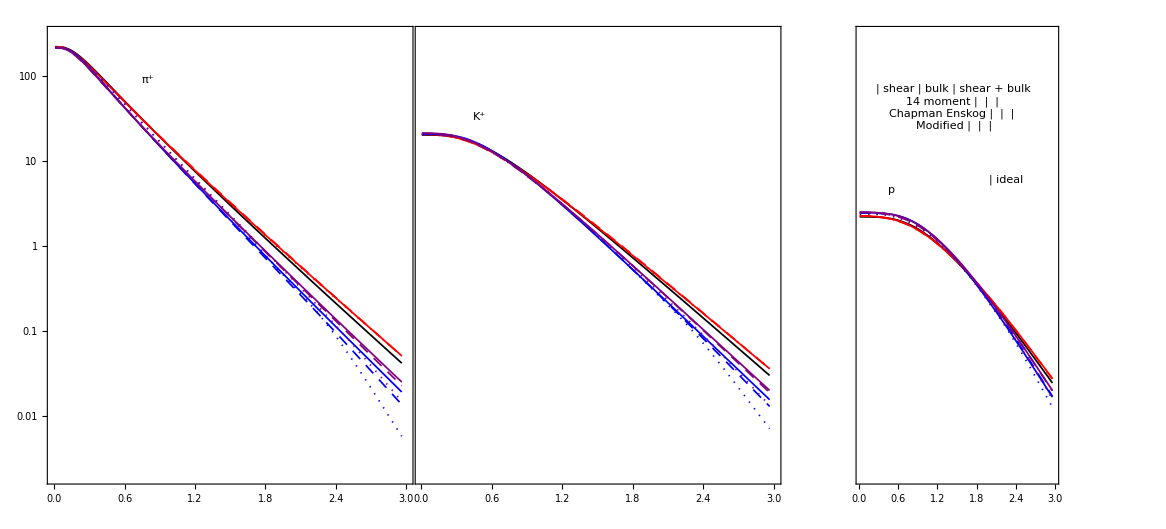
-Graphics-p_T (GeV)

```mathematica
SetDirectory@NotebookDirectory[];


pion = {idealπ,shear14π,shearCEπ,shearmodπ,bulk14π,bulkCEπ,bulkmodπ,shearbulk14π,shearbulkCEπ,shearbulkmodπ};
kaon= {idealK,shear14K,shearCEK,shearmodK,bulk14K,bulkCEK,bulkmodK,shearbulk14K,shearbulkCEK,shearbulkmodK};
proton={idealp,shear14p,shearCEp,shearmodp,bulk14p,bulkCEp,bulkmodp,shearbulk14p,shearbulkCEp,shearbulkmodp};

ratiopion = {ratioidealπ,ratioshear14π,ratioshearCEπ,ratioshearmodπ,ratiobulk14π,ratiobulkCEπ,ratiobulkmodπ,ratioshearbulk14π,ratioshearbulkCEπ,ratioshearbulkmodπ};
ratiokaon= {ratioidealK,ratioshear14K,ratioshearCEK,ratioshearmodK,ratiobulk14K,ratiobulkCEK,ratiobulkmodK,ratioshearbulk14K,ratioshearbulkCEK,ratioshearbulkmodK};
ratioproton={ratioidealp,ratioshear14p,ratioshearCEp,ratioshearmodp,ratiobulk14p,ratiobulkCEp,ratiobulkmodp, ratioshearbulk14p,ratioshearbulkCEp,ratioshearbulkmodp};



(*style={Directive[Black,AbsoluteThickness[1.5]],
Directive[Red,AbsoluteThickness[1.25],Dotted],Directive[Red,AbsoluteThickness[1.25],AbsoluteDashing[{6,5}]],Directive[Red,AbsoluteThickness[1.25]],Directive[Blue,AbsoluteThickness[1.25],Dotted],Directive[Blue,AbsoluteThickness[1.25],AbsoluteDashing[{6,5}]],Directive[Blue,AbsoluteThickness[1.25]]};*)

style={Directive[Black,AbsoluteThickness[1.25]],
Directive[Red,AbsoluteThickness[1.25],AbsoluteDashing[{1,5}]],Directive[Red,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[Red,AbsoluteThickness[1.25]],Directive[Blue,AbsoluteThickness[1.25],AbsoluteDashing[{1,5}]],Directive[Blue,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[Blue,AbsoluteThickness[1.25]],
Directive[Purple,AbsoluteThickness[1.25],AbsoluteDashing[{1,5}]],Directive[Purple,AbsoluteThickness[1.25],AbsoluteDashing[{8,6}]],Directive[Purple,AbsoluteThickness[1.25]]};

styledf={Directive[Black,AbsoluteThickness[2]],
Directive[Red,AbsoluteThickness[2],AbsoluteDashing[{1,5}]],Directive[Red,AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[Red,AbsoluteThickness[2]],Directive[Blue,AbsoluteThickness[2],AbsoluteDashing[{1,5}]],Directive[Blue,AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[Blue,AbsoluteThickness[1.5]],
Directive[Purple,AbsoluteThickness[2],AbsoluteDashing[{1,5}]],Directive[Purple,AbsoluteThickness[2],AbsoluteDashing[{8,6}]],Directive[Purple,AbsoluteThickness[2]]};

(*legenddf=Panel[Grid[{{Graphics[{style[[1]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["ideal",FontSize->14,FontFamily->"Arial"]},
{Graphics[{style[[2]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["shear mod",FontSize->14,FontFamily->"Arial"]},
{Graphics[{style[[3]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["shear CE",FontSize->14,FontFamily->"Arial"]},
{Graphics[{style[[4]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["shear 14",FontSize->14,FontFamily->"Arial"]},
{Graphics[{style[[5]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["bulk mod",FontSize->14,FontFamily->"Arial"]},
{Graphics[{style[[6]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["bulk CE",FontSize->14,FontFamily->"Arial"]},
{Graphics[{style[[7]],Line[{{0,0},{1,0}}]},ImageSize->26,AspectRatio->0.2],Style["bulk 14",FontSize->14,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];*)

legendπ=Panel[Grid[{{Style["π^+",FontSize->20,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];
legendK=Panel[Grid[{{Style["K^+",FontSize->20,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];
legendp=Panel[Grid[{{Style["p",FontSize->20,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];

dfsize=40;

legendideal = Panel[Grid[{{Graphics[{styledf[[1]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Style["ideal",FontSize->14,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];

legenddf=Panel[Grid[{{"",Style["shear",FontSize->14,FontFamily->"Arial"],Style["bulk",FontSize->14,FontFamily->"Arial"],Style["shear + bulk",FontSize->14,FontFamily->"Arial"]},

{Style["14 moment",FontSize->14,FontFamily->"Arial"],Graphics[{styledf[[2]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[5]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[8]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2]},

{Style["Chapman Enskog",FontSize->14,FontFamily->"Arial"],Graphics[{styledf[[3]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[6]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[9]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2]},

{Style["Modified",FontSize->14,FontFamily->"Arial"],Graphics[{styledf[[4]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[7]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Graphics[{styledf[[10]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2]}(*,

{"","",Graphics[{styledf[[1]],Line[{{0,0},{1,0}}]},ImageSize->dfsize,AspectRatio->0.2],Style["ideal",FontSize->11,FontFamily->"Arial"]}*)}],Background->White,FrameMargins->0];

s ={0.0095,0};
l={0.016,0};

dNticks= {{2.0*10^-3,"",s},{3.0*10^-3,"",s},{4.0*10^-3,"",s},{5.0*10^-3,"",s},{6.0*10^-3,"",s},{7.0*10^-3,"",s},{8.0*10^-3,"",s},{9.0*10^-3,"",s},{0.01,"0.01",l},
{2.0*10^-2,"",s},{3.0*10^-2,"",s},{4.0*10^-2,"",s},{5.0*10^-2,"",s},{6.0*10^-2,"",s},{7.0*10^-2,"",s},{8.0*10^-2,"",s},{9.0*10^-2,"",s},{0.1,"0.1",l},
{2.0*10^-1,"",s},{3.0*10^-1,"",s},{4.0*10^-1,"",s},{5.0*10^-1,"",s},{6.0*10^-1,"",s},{7.0*10^-1,"",s},{8.0*10^-1,"",s},{9.0*10^-1,"",s},{1,"1",l},
{2.0*10^-0,"",s},{3.0*10^-0,"",s},{4.0*10^-0,"",s},{5.0*10^-0,"",s},{6.0*10^-0,"",s},{7.0*10^-0,"",s},{8.0*10^-0,"",s},{9.0*10^-0,"",s},{10,"10",l},
{2.0*10^1,"",s},{3.0*10^1,"",s},{4.0*10^1,"",s},{5.0*10^1,"",s},{6.0*10^1,"",s},{7.0*10^1,"",s},{8.0*10^1,"",s},{9.0*10^1,"",s},{100,"100",l},{200,"",s}};

dNticksnone = {{2.0*10^-3,"",s},{3.0*10^-3,"",s},{4.0*10^-3,"",s},{5.0*10^-3,"",s},{6.0*10^-3,"",s},{7.0*10^-3,"",s},{8.0*10^-3,"",s},{9.0*10^-3,"",s},{0.01,"",l},
{2.0*10^-2,"",s},{3.0*10^-2,"",s},{4.0*10^-2,"",s},{5.0*10^-2,"",s},{6.0*10^-2,"",s},{7.0*10^-2,"",s},{8.0*10^-2,"",s},{9.0*10^-2,"",s},{0.1,"",l},
{2.0*10^-1,"",s},{3.0*10^-1,"",s},{4.0*10^-1,"",s},{5.0*10^-1,"",s},{6.0*10^-1,"",s},{7.0*10^-1,"",s},{8.0*10^-1,"",s},{9.0*10^-1,"",s},{1,"",l},
{2.0*10^-0,"",s},{3.0*10^-0,"",s},{4.0*10^-0,"",s},{5.0*10^-0,"",s},{6.0*10^-0,"",s},{7.0*10^-0,"",s},{8.0*10^-0,"",s},{9.0*10^-0,"",s},{10,"",l},
{2.0*10^1,"",s},{3.0*10^1,"",s},{4.0*10^1,"",s},{5.0*10^1,"",s},{6.0*10^1,"",s},{7.0*10^1,"",s},{8.0*10^1,"",s},{9.0*10^1,"",s},{100,"",l},{200,"",s}};

a=30;
b=30;
ratiopionplot=ListPlot[ratiopion,PlotRange->{{0.00,3.0},{0,1.25}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->190,AspectRatio->0.9,PlotLabel->Style["viscous:ideal ratio",FontSize->14,FontFamily->"Arial",Black],PlotStyle->style];

ratiokaonplot=ListPlot[ratiokaon,PlotRange->{{0.00,3.0},{0,1.25}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->190,AspectRatio->0.9,PlotLabel->Style["viscous:ideal ratio",FontSize->14,FontFamily->"Arial",Black],PlotStyle->style];
ratioprotonplot=ListPlot[ratioproton,PlotRange->{{0.00,3.0},{0,1.25}},Frame->True,FrameStyle->Black,RotateLabel->True,BaseStyle->{FontSize->12},Joined->True,InterpolationOrder->2,ImageSize->190,AspectRatio->0.9,PlotLabel->Style["viscous:ideal ratio",FontSize->14,FontFamily->"Arial",Black],PlotStyle->style];

spectra=Panel[GraphicsGrid[{{

ListLogPlot[pion,PlotRange->{{0.0,3},{2.*10^-3,300}},Frame->True,FrameStyle->Black,FrameTicks->{{dNticks,dNticksnone},{Automatic,All}},BaseStyle->{FontSize->14},Joined->True,InterpolationOrder->2,ImageSize->450,AspectRatio->1.15,PlotStyle->style,Epilog->{Inset[legendπ,{0.8,4.5}],Inset[ratiopionplot,{0.95,-3.2}]}, ImagePadding->{{a,b},{Automatic,Automatic}}],

ListLogPlot[kaon,PlotRange->{{0.01,3.0},{2.*10^-3,300}},Frame->True,FrameStyle->Black,FrameTicks->{{dNticksnone,dNticksnone},{True,All}},Joined->True,BaseStyle->{FontSize->14},InterpolationOrder->2,ImageSize->450,AspectRatio->1.15,PlotStyle->style,Epilog->{Inset[legendK,{0.5,3.5}],Inset[ratiokaonplot,{0.95,-3.2}]},ImagePadding->{{a,b},{Automatic,Automatic}}],

ListLogPlot[proton,PlotRange->{{0.01,3.0},{2.*10^-3,300}},Frame->True,FrameStyle->Black,FrameTicks->{{dNticksnone,dNticks},{True,All}},BaseStyle->{FontSize->14},Joined->True,InterpolationOrder->2,ImageSize->450,AspectRatio->1.15,PlotStyle->style,Epilog->{Inset[legendp,{0.5,1.5}],Inset[ratioprotonplot,{0.95,-3.2}],Inset[legenddf,{1.45,3.75}],Inset[legendideal,{2.25,1.8}]},ImagePadding->{{a,b},{Automatic,Automatic}}]

}},Spacings->{-65.2,0},PlotLabel->Style["(dN/(2  π SubscriptBox[p, T] SubscriptBox[dp, T] dy))_(|_(y = 0))",FontSize->26,FontFamily->"Arial",Black]],{Style["p_T (GeV)",FontFamily->"Arial",FontSize->18]},{{Bottom,Center}},Appearance->"Frameless",FrameMargins->0,Background->White]
Export["modified_spectra_500MeV.pdf",spectra];
```